```mathematica
(*Тут генерация точек, и так сойдет. И для двумерных пока*)
SeedRandom[42];
R=3;(*размерность пространства*)
coefNonZero="0000000";(*начальные состояния атомов  "110000110000" *)
n=StringLength[coefNonZero]; (*количество атомов*)
size=n;
points=RandomVariate[NormalDistribution[0,2 Pi],{n,R}];(*координаты атомов*)
distAr=ConstantArray[0,{n,n}]; (*массив расстояний между точками/атомами*)
g=1; (*скорость взаимодействия/перехода (?) *)
k=1; (*какая-то константа 2 Pi/R*)
Do[Do[
distAr[[i]][[j]]=EuclideanDistance[points[[i]],points[[j]]]
,{j,1,n}],{i,1,n}]
points
```

{{-6.35889,5.19204,-8.75742},{2.61958,-1.65869,6.60307},{2.64878,9.42761,9.28613},{-1.57115,-9.81352,-3.2283},{0.140062,-5.12017,3.4456},{-0.0656954,4.74314,1.16601},{-2.51489,8.41912,-5.54493}}

```mathematica
(*тут создание матриц, перепутывающих 2 каких-то атома с номерами (i1, i2) в системе из size атомов*)
Createf[size_,i1_,i2_,distr_]:=
Module[{num,tmp,copynum,idx1,idx2},
f=ConstantArray[0,{2^size,2^size}];
If[i1>n ||i2>n||i1==i2,Print["Ты облажался с индексами"];Return[];];
Do[
num =IntegerDigits[i,2,size];
copynum=num;
tmp=num[[i1]];
num[[i1]]=num[[i2]];
num[[i2]]=tmp;
idx1=FromDigits[copynum,2]+1;
idx2=FromDigits[num,2]+1;
If[idx1<idx2, f[[idx1,idx2]]= Exp[I k distr], f[[idx1,idx2]]= Exp[-I k distr]];
,{i,0,2^size-1}];
Return[f]
]
```

```mathematica
Createv[size_]:=Module[{lmat,eye2,tmp},
tmp=ConstantArray[1,1];
(*lmat={{0,Exp[I k xl]},{Exp[-I k xl],0}};*)
eye2=IdentityMatrix[2];
tmpArr={};
Do[
tmp=ConstantArray[1,1];
Do[
If[idx==l,tmp=KroneckerProduct[tmp,{{0,Exp[I k points[[l,1]]]},{Exp[-I k points[[l,1]]],0}}],tmp=KroneckerProduct[tmp,eye2]];
,{idx,1,size}];
AppendTo[tmpArr,tmp]
,{l,1,size}];
g Total[tmpArr]
]
```

```mathematica
Norm[Createv[8]-ConjugateTranspose[Createv[8]]]
```

0.

```mathematica
size=n
With[{temp=Createv[size]},
v0= ConstantArray[0,2^size];
v0[[1]]=1;
solVn=(MatrixExp[I temp it].v0);
(*t1=Table[{it,Abs[solVn[[idx]]]^2},{idx,1,2^size},{it,0,2Pi,2 Pi/1000}];
ListPlot[t1,Joined->True,PlotRange->All,PlotLegends->Automatic]*)
]
```

7

```mathematica
solVn[[1]][[1]]
```

(0.013077+0.0077001 ⅈ) ((0.+0. ⅈ)-(3.09914+1.27862 ⅈ) (ⅇ^(-2.8588×10^-16 it) Cos[2.78275×10^-17 it]-ⅈ ⅇ^(-2.8588×10^-16 it) Sin[2.78275×10^-17 it]))

```mathematica
GetRedused[sol_,size_,part_]:=Module[{list1},
list1=Subsets[Range[1,size],{size-part}];
Total[Table[ResourceFunction["MatrixPartialTrace"][sol,list1[[idxL]],2],{idxL, 1, Length[list1]}]]/Length[list1]
]
```

{7.51563,Null}

---

{17.6719,Null}

---

{0.,Null}

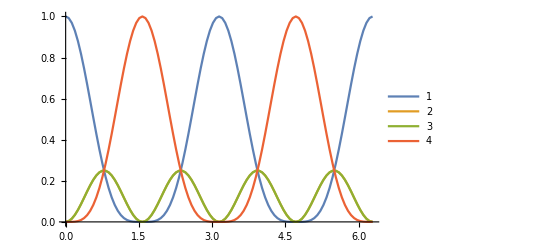

```mathematica
Timing[
matSolVn = Table[TensorProduct[solVn,ConjugateTranspose[solVn]],{it,0,2 Pi,2Pi/100}];
]
Print["---"]
Timing[
redVn = Table[GetRedused[matSolVn[[idx]],size,2],{idx,1,Length[matSolVn]}];
]
Print["---"]
Timing[
t1=Table[{2Pi/100 (k-1),redVn[[k,idx,idx]]},{idx,1,4},{k,1,Length[redVn]}];
]
ListPlot[t1,Joined->True,PlotRange->All,PlotLegends->Automatic]
```

```mathematica
t1[[1]]
```

{{0,590.183+0. ⅈ},{π/50,587.494+0. ⅈ},{π/25,591.294+0. ⅈ},{(3 π)/50,594.543+0. ⅈ},{(2 π)/25,592.491+0. ⅈ},{π/10,593.77+0. ⅈ},{(3 π)/25,590.72+0. ⅈ},{(7 π)/50,589.919+0. ⅈ},{(4 π)/25,588.876+0. ⅈ},{(9 π)/50,588.78+0. ⅈ},{π/5,589.831+0. ⅈ},{(11 π)/50,584.324+0. ⅈ},{(6 π)/25,583.553+0. ⅈ},{(13 π)/50,582.332+0. ⅈ},{(7 π)/25,585.241+0. ⅈ},{(3 π)/10,580.608+0. ⅈ},{(8 π)/25,579.116+0. ⅈ},{(17 π)/50,579.188+0. ⅈ},{(9 π)/25,585.899+0. ⅈ},{(19 π)/50,575.819+0. ⅈ},{(2 π)/5,581.406+0. ⅈ},{(21 π)/50,582.163+0. ⅈ},{(11 π)/25,576.025+0. ⅈ},{(23 π)/50,574.069+0. ⅈ},{(12 π)/25,576.971+0. ⅈ},{π/2,577.564+0. ⅈ},{(13 π)/25,571.024+0. ⅈ},{(27 π)/50,578.131+0. ⅈ},{(14 π)/25,575.075+0. ⅈ},{(29 π)/50,580.215+0. ⅈ},{(3 π)/5,567.193+0. ⅈ},{(31 π)/50,580.125+0. ⅈ},{(16 π)/25,579.499+0. ⅈ},{(33 π)/50,579.602+0. ⅈ},{(17 π)/25,587.137+0. ⅈ},{(7 π)/10,585.576+0. ⅈ},{(18 π)/25,580.361+0. ⅈ},{(37 π)/50,577.435+0. ⅈ},{(19 π)/25,580.592+0. ⅈ},{(39 π)/50,586.237+0. ⅈ},{(4 π)/5,589.971+0. ⅈ},{(41 π)/50,582.427+0. ⅈ},{(21 π)/25,585.36+0. ⅈ},{(43 π)/50,586.651+0. ⅈ},{(22 π)/25,585.826+0. ⅈ},{(9 π)/10,588.433+0. ⅈ},{(23 π)/25,587.643+0. ⅈ},{(47 π)/50,584.723+0. ⅈ},{(24 π)/25,586.543+0. ⅈ},{(49 π)/50,590.774+0. ⅈ},{π,591.475+0. ⅈ},{(51 π)/50,590.88+0. ⅈ},{(26 π)/25,591.498+0. ⅈ},{(53 π)/50,591.281+0. ⅈ},{(27 π)/25,589.425+0. ⅈ},{(11 π)/10,593.414+0. ⅈ},{(28 π)/25,582.384+0. ⅈ},{(57 π)/50,590.519+0. ⅈ},{(29 π)/25,587.818+0. ⅈ},{(59 π)/50,578.522+0. ⅈ},{(6 π)/5,581.291+0. ⅈ},{(61 π)/50,577.595+0. ⅈ},{(31 π)/25,583.496+0. ⅈ},{(63 π)/50,582.036+0. ⅈ},{(32 π)/25,575.417+0. ⅈ},{(13 π)/10,581.164+0. ⅈ},{(33 π)/25,579.898+0. ⅈ},{(67 π)/50,579.552+0. ⅈ},{(34 π)/25,578.934+0. ⅈ},{(69 π)/50,575.792+0. ⅈ},{(7 π)/5,578.416+0. ⅈ},{(71 π)/50,579.185+0. ⅈ},{(36 π)/25,578.229+0. ⅈ},{(73 π)/50,574.636+0. ⅈ},{(37 π)/25,582.117+0. ⅈ},{(3 π)/2,577.172+0. ⅈ},{(38 π)/25,576.433+0. ⅈ},{(77 π)/50,568.973+0. ⅈ},{(39 π)/25,577.494+0. ⅈ},{(79 π)/50,580.009+0. ⅈ},{(8 π)/5,582.768+0. ⅈ},{(81 π)/50,579.742+0. ⅈ},{(41 π)/25,579.68+0. ⅈ},{(83 π)/50,580.05+0. ⅈ},{(42 π)/25,581.221+0. ⅈ},{(17 π)/10,577.067+0. ⅈ},{(43 π)/25,575.764+0. ⅈ},{(87 π)/50,585.401+0. ⅈ},{(44 π)/25,586.426+0. ⅈ},{(89 π)/50,586.585+0. ⅈ},{(9 π)/5,583.955+0. ⅈ},{(91 π)/50,584.724+0. ⅈ},{(46 π)/25,578.997+0. ⅈ},{(93 π)/50,587.234+0. ⅈ},{(47 π)/25,588.392+0. ⅈ},{(19 π)/10,585.971+0. ⅈ},{(48 π)/25,587.18+0. ⅈ},{(97 π)/50,590.203+0. ⅈ},{(49 π)/25,579.063+0. ⅈ},{(99 π)/50,592.159+0. ⅈ},{2 π,591.116+0. ⅈ}}

```mathematica
GetFMat[size_]:=Module[{allGroups,idxArray,listOfAllPairIdx},
allGroups =Subsets[Range[1,n],{size}]; (*всевозможные группы размера size*)
Do[
idxArray=allGroups[[idxGroup]]; (*индексы в исходной нумерации атомов*)
listOfAllPairIdx=Subsets[Range[1,size],{2}];(*список всех не повторяющихся элементов по 2 индекса, для генерачии матриц f_{i1,i2}*)
w=Total[Table[
1/distAr[[idxArray[[listOfAllPairIdx[[idxPair,1]]]],idxArray[[listOfAllPairIdx[[idxPair,2]]]]]]  (Createf[size,listOfAllPairIdx[[idxPair,1]],listOfAllPairIdx[[idxPair,2]],distAr[[idxArray[[listOfAllPairIdx[[idxPair,1]]]],idxArray[[listOfAllPairIdx[[idxPair,2]]]]]]]),{idxPair,Length[listOfAllPairIdx]}]];
,{idxGroup,1, Length[allGroups]}];
Return[w]
]
```

```mathematica
size=n;
(*2,3,5 совпадает 4,6,7*)
With[{temp=Createv[size],temp1=GetFMat[size]},
v0= ConstantArray[0,2^size];
v0[[1]]=1;
solAdd=(MatrixExp[I (temp+temp1) it].v0);
(*t1=Table[{it,Abs[solAdd[[idx]]]^2},{idx,1,2^size},{it,0,2Pi,2 Pi/1000}];
ListPlot[t1,Joined->True,PlotRange->All,PlotLegends->Automatic]*)
]
```

{9.60938,Null}

{19.4531,Null}

{0.,Null}

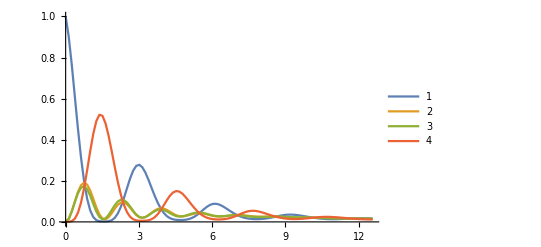

```mathematica
Timing[
matSolAdd =Table[ TensorProduct[solAdd,ConjugateTranspose[solAdd]],{it,0,4 Pi,2Pi/50}];
]
Timing[
redAdd =  Table[GetRedused[matSolAdd[[idx]],size,2],{idx,1,Length[matSolAdd]}];
]
Timing[
t2=Table[{2Pi/50 (k-1),redAdd[[k,idx,idx]]},{idx,1,4},{k,1,Length[redAdd]}];
]
ListPlot[t2,Joined->True,PlotRange->All,PlotLegends->Automatic]
```

```mathematica
Norm[Createv[size]+GetFMat[size]-ConjugateTranspose[Createv[size]+GetFMat[size]]]
```

0.844923

```mathematica
Norm[GetFMat[size]-ConjugateTranspose[GetFMat[size]]]
```

0.844923